# The C.W. Mills Award and can one measure “Thank You?”

## Henry Hyunsuk Kim

## Mentor, Bob Nachbar WSS 2019

### Introduction

Just as Auguste Comte, Karl Marx, Max Weber, and Emile Durkheim are key figures in the discipline of sociology in general, C.W. Mills is a key person in U.S. contexts (as are W.E.B. Du Bois and Charlotte Perkins Gilman). To study anything through a “sociological” lens requires the utilization of Mills’ “sociological imagination.” Simply put, this is identifying when certain personal problems are structural ills. Unsurprisingly, there is an annual book award in his honor, the “C. Wright Mills Award.” Though the field of bibliometrics is replete with citation analysis, a gap may exist regarding acknowledgements. Thus, my exploratory project concerns ascertaining what patterns may emerge with respect to acknowledgments in each and all of the books that have won the Mills Award to date. With the help of two RAs (Julian Petoske and Zury Rodriguez), the following book information was entered into an Excel spreadsheet: year of publication, title, author(s), persons acknowledged, author’s institution at the time of publication, where the author(s) completed her or his degrees (undergraduate and PhD), and the publisher. The data from the Excel file was then cleaned and analyzed via Mathematica at the 2019 Wolfram Summer Program with the invaluable help of two key Wolfram personnel (Bob Nachbar and Jesse Friedman). There was a total of 63 books, 68 authors (5 books were co-written), and a total of 2530 acknowledgments whereby 2369 were unique acknowledgements, spanning the years from 1964 through 2017.

### Importing, Cleaning, and Preparing the Data

```mathematica
bookwinnersDataset=Import["C:\\Users\\hekim\\Box Sync\\wheaton\\Papers\\Works in Progress\\Testing 4.10 II.xlsx",{"Dataset",1},HeaderLines->1];
```

```mathematica
bookWinners=Normal[bookwinnersDataset];
Short[%,5]
```

{<|Year→2017.,Book Title→Juarez Girls Rising: Transformative Education in Times of Dystopia,Author→Claudia G.Cervantes-Soon,Academic Acknowledgements→Angela Valenzuela,Autho…ation→…,Author UG→UT, El Paso,Author PhD→UT, Austin,Publisher→University of Minnesota|>,«2537»,<|«1»|>}

```mathematica
bookWinners=MapAt[Floor,bookWinners,{All,Key["Year"]}];
```

```mathematica
Dataset[bookWinnersClean=DeleteCases[bookWinners,"",{2}]];
```

```mathematica
gatheredBookWinners=GatherBy[bookWinnersClean,#["Book Title"]&];
Short[%,4]
```

{{«1»},{«1»},«59»,{<|Year→1965,Book Title→The New Utopians,Author→Robert Boguslaw,Academic Acknowledgements→…,«1»,Author UG→Brooklyn College,Author PhD→New York University,Publisher→Prentice-Hall, Inc.|>,«18»},{«1»}}

```mathematica
Dataset[mergedBookWinners=Merge[#,Union]&/@gatheredBookWinners];
```

```mathematica
Dataset[condensedBookWinners=MapIndexed[(If[
First[#2]===Key["Academic Acknowledgements"],
#1,
First[#1]
]&),#]&/@mergedBookWinners];
```

```mathematica
integerYearBookWinners=MapAt[Round,condensedBookWinners,{All,1}];
```

```mathematica
authors = integerYearBookWinners[[2;;,3]];
```

```mathematica
splitAuthors[authorString_String]:=StringSplit[authorString, " and "]
```

```mathematica
Dataset[integerYearBookWinnersSplitAuthors=MapAt[splitAuthors,integerYearBookWinners,{All,"Author"}]];
```

```mathematica
yearsRange=MinMax[Sort@integerYearBookWinnersSplitAuthors[[All,"Year"]]]
```

{1964,2017}

```mathematica
totalBooks = integerYearBookWinnersSplitAuthors[[All, "Book Title"]]//Length
```

63

```mathematica
totalAuthors =integerYearBookWinnersSplitAuthors[[All, "Author"]]//Flatten//Length
```

68

```mathematica
totalAcnowledgments =integerYearBookWinnersSplitAuthors[[All, "Academic Acknowledgements"]]//Flatten//Length
```

2530

```mathematica
uniqueTotalAcnowledgments =integerYearBookWinnersSplitAuthors[[All, "Academic Acknowledgements"]]//Flatten//DeleteDuplicates//Length
```

2369

```mathematica
Keys@First@bookWinners//Column
```

Year
Book Title
Author
Academic Acknowledgements
Authors' Institution @ Publication
Author UG
Author PhD
Publisher

```mathematica
bookWinners=MapAt[Floor,bookWinners,{All,Key["Year"]}];
```

```mathematica
gatheredBookWinners=GatherBy[bookWinnersClean,#["Book Title"]&];
```

```mathematica
bookWinnersForYear[year_]:=Select[integerYearBookWinnersSplitAuthors,#Year===year&]
```

```mathematica
bookWinnersBetweenYears[from_,to_]:=Select[integerYearBookWinnersSplitAuthors,Between[#Year,{from,to}]&]
```

```mathematica
ClearAll[removeDisconnectedNetworks]
removeDisconnectedNetworks[edges:{(_UndirectedEdge|_DirectedEdge)..}]:=removeDisconnectedNetworks[Graph[edges, VertexLabels -> "Name",ImageSize -> 500]]
removeDisconnectedNetworks[graph_Graph]:=Module[{
components,
maincomponentvertices
},
components=ConnectedComponents[UndirectedGraph[graph]];
maincomponentvertices=MaximalBy[components,Length];
Subgraph[graph,maincomponentvertices]
]
```

Below is a graph of the entire list of winners and persons they acknowledged (through 2017). The graph depicts the core nework because the disconnected sub-graphs were removed in the hopes of providing better analyses.

```mathematica
edgesFromWinners[winners_]:=Join@@(Join@@Outer[DirectedEdge,Sequence@@Values@#]&)/@winners[[All,{3,4}]]
```

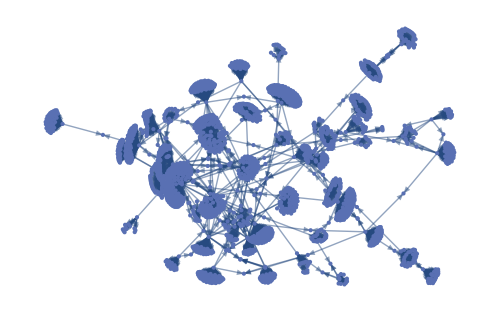

```mathematica
graphsPerYear=AssociationMap[
Graph[removeDisconnectedNetworks[edgesFromWinners[bookWinnersForYear[#]]], VertexLabels -> "Name",ImageSize -> 500]
&,Sort@integerYearBookWinnersSplitAuthors[[All,"Year"]]];
accumulatingGraphs=AssociationMap[
Graph[removeDisconnectedNetworks[edgesFromWinners[bookWinnersBetweenYears[yearsRange[[1]],#]]], VertexLabels -> "",ImageSize -> 500]
&,Range@@yearsRange];
accumulatingGraphs[2017]
```

```mathematica
ClearAll[gleanWellConnectedPersons]
Options[gleanWellConnectedPersons]={"count"->15,"measure"->BetweennessCentrality};
gleanWellConnectedPersons[graph_,OptionsPattern[]]:=
Module[{measure,count,namesAndCentralities,sortedList,topPersons},
measure=OptionValue["measure"];
count=OptionValue["count"];
namesAndCentralities=Thread[{VertexList[graph],measure[graph]}];
sortedList=ReverseSortBy[namesAndCentralities,Last];
topPersons=Take[sortedList,UpTo[count]];
DeleteCases[topPersons,{_,0.}]
]
```

### Preliminary Questions and Answers

Where was the author when the book was published? 
Further inquiry needs to ascertain what properties of homophily and propinquity may have fostered social reproduction with respect to the authors’ academic affiliations. Interestingly, 12 authors won the award while employed in the UC system, respectively, Berkeley (10), San Diego (3), Santa Barbara (1), and Santa Cruz (1).

```mathematica
authorsSplitAtPublication = integerYearBookWinnersSplitAuthors[[All,"Authors' Institution @ Publication"]];
authorsSplitAtPublication;
Tally[%];
ReverseSortBy[%,Last]//TableForm
PieChart[Apply[Labeled,Reverse[%,2],{1}]]
```

UC, Berkeley | 7
Harvard University | 5
Columbia University | 5
Princeton University | 4
University of Chicago | 3
UC, San Diego | 3
University of Toronto (CAN) | 2
Massachusetts Institute of Technology | 2
Graduate Center, CUNY | 2
USC | 1
University of Virginia | 1
University of Southern Maine | 1
University of Oregon | 1
University of Louisville | 1
University of Cincinnati | 1
University of Arizona | 1
UNC, Chapel Hill | 1
UC, Santa Cruz | 1
UC, Santa Barbara | 1
The American Socialist | 1
SUNY, Stony Brook | 1
Stockholm University | 1
Southern Illinois University | 1
San Francisco State University | 1
Rutgers University | 1
Northern Illinois University | 1
Northeastern University | 1
New School for Social Research | 1
National Institute of Mental Health | 1
National Bureau of Economic Research | 1
Mills College | 1
Michigan State University | 1
Hong Kong University of Science and Technology | 1
George Mason University | 1
Foothills College | 1
Brooklyn College | 1
Brandeis University | 1
Boston University | 1
American Universty | 1

-Graphics-

Where the did authors go to college?
No patterns seem to emerge with respect to where the authors went to college. 4 went to Harvard, a total of 9 went to an Ivy League school, and 6 went to a UC school. Although this does not necessarily disprove social reproduction, it does suggest that where one went to college may not necessarily be a good “predictor” in whether one wins the Mills Award. Unfortunately, this project was not able to ascertain the authors’ majors when they graduated from college.

```mathematica
authorsSplitAtunderG=integerYearBookWinnersSplitAuthors[[All,"Author UG"]];
authorsSplitAtunderG;
Tally[%];
ReverseSortBy[%,Last]//TableForm
PieChart[Apply[Labeled,Reverse[%,2],{1}]]
```

Harvard University | 4
UC, Santa Cruz | 3
UC, San Diego | 3
Columbia University | 3
University of Chicago | 2
Oberlin College | 2
Colorado College | 2
Carleton College | 2
Brandeis University | 2
Wilberforce University | 1
Western Michigan University | 1
UW, Madison | 1
UT, El Paso | 1
University of Tennessee, Knoxville  | 1
University of Sussex (UK) | 1
University of Ottawa (CA) | 1
University of Michigan | 1
University of Illinois, Urbana-Champaign | 1
University of Guelph (CAN) | 1
University of Denver | 1
University of Cape Town | 1
University of Barcelona | 1
UNC, Chapel Hill | 1
Temple University | 1
Swarthmore College | 1
Stockholm University | 1
Smith College | 1
Rutgers University | 1
Reed College | 1
Radcliffe College | 1
Princeton University | 1
Ohio State University | 1
Occidental College | 1
Northwestern University | 1
New School of Social Research | 1
Michigan State University | 1
Maryknoll College | 1
Karl Marx University of Economics | 1
Haverford College | 1
Georgia Institute of Technology | 1
George Washington Unniversity | 1
Cornell University | 1
Colby College | 1
City College of New York | 1
Chinese University of Hong Kong | 1
Bryn Mawr College | 1
Brooklyn College | 1
Barnard College | 1
Albany State Teachers College | 1

-Graphics-

Where did the author get her/his PhD? 
Whereas an undergraduate degree may not have had much bearing on winning the Mills Award, where one received her or his PhD seems to have mattered. 11 winners went to Harvard. (Is there a way to extract the Ivy League Schools and tabulate them?) Unfortunately, this project did not include the major sub-themes the authors studied for the PhD, nor did it include the lead dissertation advisor and respective committee members.

```mathematica
authorsAtPhd=integerYearBookWinnersSplitAuthors[[All,"Author PhD"]];
authorsAtPhd;
Tally[%];
ReverseSortBy[%,Last]//TableForm
PieChart[Apply[Labeled,Reverse[%,2],{1}]]
```

Harvard University | 11
UC, Berkeley | 5
University of Chicago | 4
Columbia University | 4
UW, Madison | 3
Northwestern University | 3
Yale University | 2
Washington University in St. Louis | 2
Princeton University | 2
Missing[KeyAbsent,Author PhD] | 1
Washington State University | 1
UT, Austin | 1
University of Pensylvania | 1
University of Paris | 1
University of Michigan | 1
University of London, SOAS | 1
University of Illinois, Urbana-Champaign | 1
University of Alberta | 1
UC, Santa Barbara | 1
UC, San Francisco | 1
UC, San Diego | 1
UC, Irvine | 1
UC, Davis | 1
SUNY, Stony Brook | 1
Stockholm University | 1
Stanford University | 1
Northwestern University  | 1
New York University | 1
MIT | 1
Massachusetts Institute of Technology | 1
Hungarian Academy of Sciences | 1
Harvard Medical School | 1
Graduate Center, CUNY | 1
Compultense University of Madrid | 1
Catholic University | 1
Brandeis University | 1

-Graphics-

Who was the Publisher? 
One publisher clearly stood out among the others, the University of California Press, which accounted for 13 winners. Unfortunately, this study did not include any information on the main editor(s) of the book winners.

```mathematica
authorsAndPub=integerYearBookWinnersSplitAuthors[[All,"Publisher"]];
authorsAndPub;
Tally[%];
ReverseSortBy[%,Last]//TableForm
PieChart[Apply[Labeled,Reverse[%,2],{1}]]
```

University of California Press | 13
University of Chicago Press | 4
Russell Sage Foundation | 4
Oxford University Press | 4
Cambridge University Press | 4
Harvard University Press | 3
Routledge | 2
Princeton University Press | 2
John Wiley & Sons, Inc. | 2
Basic Books | 2
Wisconsin University Press | 1
Westview Press | 1
Vintage Books | 1
University of Minnesota | 1
The University Press of Kentucky | 1
The MIT Press | 1
The Free Press | 1
The Belknap Press of Harvard University Press | 1
Rutgers University Press | 1
Routledge and Kegan Paul Ltd. | 1
Prentice-Hall, Inc. | 1
Prentice-Hall | 1
Monthly Review Press | 1
Little Brown | 1
Indiana University Press | 1
Farrar Straus & Giroux | 1
Duke University Press | 1
D.C. Health and Company | 1
Cornell University Press | 1
Basic Books, Inc. Publishers | 1
Basic Books, Inc. | 1
Allen Lane | 1
Aldine Publishing Company | 1

-Graphics-

### SNA Metrics

Although almost twenty different SNA metrics were ascertained, most were unusable for various reasons. Thus, the five metrics that were explored in this study were: VertexOutDegree (VOD), VertexInDegree (VID), DegreeCentrality (DC), BetweennessCentrality (BC), and MeanNeighborDegree (MND). Because this project explores how authors “thanked” someone in the preface, I decided to employ a directed graph. Accordingly, the author is the “sender” (out-degree) and the person acknowledged (or thanked) is the “recipient” (in-degree).

VOD tabulates each time an author “thanked” someone in the preface and the VID measures each time a person was “thanked.” DC is the total number of ties with a given link, and thus may account for either VOD or VID (being a winning author does not preclude being “thanked.”) BC notes how many times a node is on the shortest path between two other nodes. Thus, the greater the BC score, the greater the likelihood that it fills a “structural hole.” This is important regarding the flow of information in networks. Finally, MND provides the average number of nodes that are connected to a particular node in question.

### Top score per given year

Below are the ListLinePlots for the single highest specified SNA metric per respective year. VOD, DC, and MND show relatively stable growth until the end of the 20th century, where they spike in 1999.  BC shows a regular “step” growth with spikes at 2004 (215), 2013 (370), and 2014 (512). Perhaps VID shows the most “regular” pattern of growth, except for short dip in 1982 and 1983. (BC has gaps in 1964, 1965, 1982, and 1983.) Using VOD (the large out put was suppressed, as were all subsequent outputs, respectively, using a template code: topConnectedPersonsVertexOutDegree[[All,1;;3]];) as an example, one sees the first metric in 1964 (David Matza, 20), a jump in 1970 (Jacqueline P. Wiseman, 47), and the dramatic spike in 1999 (Mitchell Duneier, 204). (Duneier’s award then makes me wonder, how much influence this had in the popularity of his   undergraduate sociology textbooks. I am receive very regular advertisements for his newest editions and... have used one of his texts for over a decade! This Mills project, via simple Mathematica analyses, have sparked a newer set of questions - the “sociological imagination”). For VID, although the scores range from 1 to 7, the person that stands out is Ann Swidler; she had the highest score from 1986 through 2007, from 2010 through 2015, and she was tied for first in 2016 and 2017. DC, as noted, could theoretically be different than the VID or VOD. Starting with the first winner in 1964, the next spike is in 1970 (Jacqueline P. Wiseman, 47), and unsurprisingly, the next jump occurs in 1999 (Mitchell Duneier, 204) and his scores moves to 205 in 2004 (this year’s winner thanked Duneier in the preface). For BC, there are the three significant spikes can be attributed to Charles Tilly in 1986 (BC, 96), Mitchell Duneier in 2004 (BC, 215), and Michele Lamont in 2015 (BC, 511.5). Finally, the spikes in the MD metric can be attributed to William Sanders in 1970 (MD, 47), Yuval Yunay in 1996 (MD, 98), and Yvonne Brown in 1999 (MD, 204).

### VertexOutDegree

{20,20,20,20,20,20,47,47,47,47,47,47,47,47,47,47,47,47,53,53,53,53,60,60,60,60,60,60,60,60,60,81,98,98,98,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204}

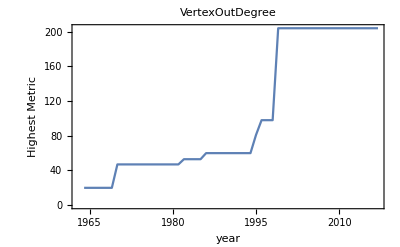

FittedModel[-14.2061+4.34622 x]

```mathematica
topConnectedPersonsVertexOutDegree=gleanWellConnectedPersons[#,"measure"->VertexOutDegree]&/@accumulatingGraphs;
yearAndSNAs=KeyValueMap[{#1,Last/@#2}&,topConnectedPersonsVertexOutDegree];
MapAt[Max,yearAndSNAs,{All,2}];
data=%;
lmfData =data[[All,2]]
ListLinePlot[MapAt[Max,yearAndSNAs,{All,2}],FrameLabel->{"year","Highest Metric"},Axes->False,Frame->True,PlotLabel->VertexOutDegree]
LinearModelFit[lmfData,{1,x},x]
```

This was used as a way to double-check my scores; I actually used the first line but included the second line to partially show the results.

```mathematica
topConnectedPersonsVertexOutDegree[[All,;;2]];
topConnectedPersonsVertexOutDegree[[;;2,1;;3]]
```

<|1964→{{David Matza,20},{William Peterson,0},{Sheldon Messinger,0}},1965→{{David Matza,20},{William Peterson,0},{Sheldon Messinger,0}}|>

### VertexInDegree

{1,1,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,2,2,3,3,4,4,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7}

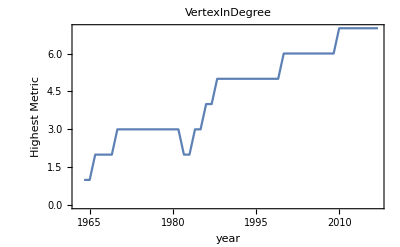

FittedModel[1.44235+0.109167 x]

```mathematica
topConnectedPersonsVertexInDegree=gleanWellConnectedPersons[#,"measure"->VertexInDegree]&/@accumulatingGraphs;
yearAndSNAs=KeyValueMap[{#1,Last/@#2}&,topConnectedPersonsVertexInDegree];
MapAt[Max,yearAndSNAs,{All,2}];
data=%;
lmfData =data[[All,2]]
ListLinePlot[MapAt[Max,yearAndSNAs,{All,2}],FrameLabel->{"year","Highest Metric"},Axes->False,Frame->True,PlotLabel->VertexInDegree]
LinearModelFit[lmfData,{1,x},x]
```

### DegreeCentrality

{20,20,21,21,21,21,47,47,47,47,47,47,47,47,47,47,47,47,53,53,53,53,60,60,60,60,60,60,60,60,60,81,98,98,98,204,204,204,204,204,205,205,205,205,205,205,205,205,205,205,205,205,205,205}

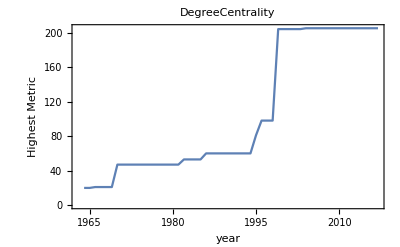

FittedModel[-14.2669+4.36055 x]

```mathematica
topConnectedPersonsDegreeCentrality=gleanWellConnectedPersons[#,"measure"->DegreeCentrality]&/@accumulatingGraphs;
yearAndSNAs=KeyValueMap[{#1,Last/@#2}&,topConnectedPersonsDegreeCentrality];
MapAt[Max,yearAndSNAs,{All,2}];
data=%;
lmfData =data[[All,2]]
ListLinePlot[MapAt[Max,yearAndSNAs,{All,2}],FrameLabel->{"year","Highest Metric"},Axes->False,Frame->True,PlotLabel->DegreeCentrality]
LinearModelFit[lmfData,{1,x},x]
```

(FYI, I am not sure why sometimes I get the output in DataSet format, then re-evaluate the code above and the one below, and get the output in association format)

### BetweennessCentrality

{-∞,-∞,18.,18.,18.,18.,35.,35.,35.,35.,35.,35.,35.,35.,35.,35.,35.,35.,-∞,-∞,30.,30.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,215.,215.,215.,215.,215.,214.,214.,214.,214.,370.,512.,511.5,511.5,511.5}

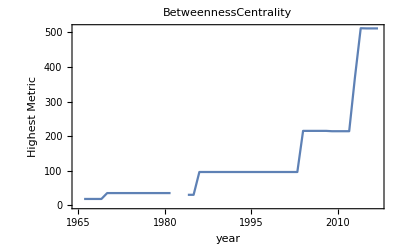

FittedModel[-62.3747+7.64411 x]

```mathematica
topConnectedPersonsBetweennessCentrality=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs;
yearAndSNAs=KeyValueMap[{#1,Last/@#2}&,topConnectedPersonsBetweennessCentrality];
MapAt[Max,yearAndSNAs,{All,2}];
data=%;
lmfData =data[[All,2]]
ListLinePlot[MapAt[Max,yearAndSNAs,{All,2}],FrameLabel->{"year","Highest Metric"},Axes->False,Frame->True,PlotLabel->BetweennessCentrality]
LinearModelFit[DeleteCases[lmfData,Except[_?NumberQ]],{1,x},x]
```

### MeanNeighborDegree

{20,20,21,21,21,21,47,47,47,47,47,47,47,47,47,47,47,47,53,53,53,53,60,60,60,60,60,60,60,60,60,81,98,98,98,204,204,204,204,204,205,205,205,205,205,205,205,205,205,205,205,205,205,205}

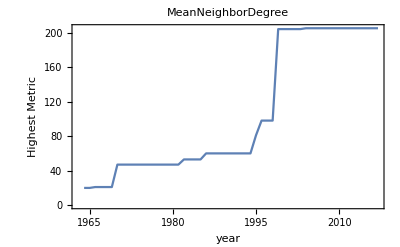

FittedModel[-14.2669+4.36055 x]

```mathematica
topConnectedPersonsMeanNeighborDegree=gleanWellConnectedPersons[#,"measure"->MeanNeighborDegree]&/@accumulatingGraphs;
yearAndSNAs=KeyValueMap[{#1,Last/@#2}&,topConnectedPersonsMeanNeighborDegree];
MapAt[Max,yearAndSNAs,{All,2}];
data=%;
lmfData =data[[All,2]]
ListLinePlot[MapAt[Max,yearAndSNAs,{All,2}],FrameLabel->{"year","Highest Metric"},Axes->False,Frame->True,PlotLabel->MeanNeighborDegree]
LinearModelFit[lmfData,{1,x},x]
```

### Testing all respective SNA metrics via All years

in this section I tried to extract all of the respective SNA metrics per node and year, and test what patterns emerged as a function of time. For example, from 1964-2017, there were 810 VertexInDegree scores. As proof of concept, I ran a simple LinearModelFit. Unfortunately, my Mathematica Language (in)abilities precluded any attempts to run more sophisticated tests. All of the five SNA metrics in this study, based on a FittedModel data analysis, evinced a slightly positive slope (BC was the highest at +.352715). It is thus not surprising that there would be a positive correlation in a simple regression since the sample epitomizes a selection bias. However, why the BC was the greatest score needs further exploration. Is this because of Ronald Burt’s “structural holes” thesis or is there evidence of Adam Grant’s “give and take”? Or perhaps there is credence to point in pop-journalist Malcolm Gladwell’s David and Goliath book, it is better to be a big fish in small pond than small fish in a big pond as pertaining to one’s undergraduate institution.

### VertexOutDegree

```mathematica
topConnectedPersonsVertexOutDegree=gleanWellConnectedPersons[#,"measure"->VertexOutDegree]&/@accumulatingGraphs//Dataset;
vertexOutDegree =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsVertexOutDegree];
allVertexOutDegree=vertexOutDegree[[All,3]];
LinearModelFit[allVertexOutDegree,{1,x},x]
Length[vertexOutDegree]
```

FittedModel[-12.039+0.124308 x]

810

### VertexInDegree

```mathematica
topConnectedPersonsVertexInDegree=gleanWellConnectedPersons[#,"measure"->VertexInDegree]&/@accumulatingGraphs//Dataset;
vertexInDegree =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsVertexInDegree];
allVertexInDegree=vertexInDegree[[All,3]];
LinearModelFit[allVertexInDegree,{1,x},x]
Length[vertexInDegree]
```

FittedModel[0.790603+0.00413942 x]

810

### Degree Centrality

```mathematica
topConnectedPersonsDegreeCentrality=gleanWellConnectedPersons[#,"measure"->DegreeCentrality]&/@accumulatingGraphs//Dataset;
vertexDegreeCentrality =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsDegreeCentrality];
allVerteDegreeCentrality=vertexDegreeCentrality[[All,3]];
LinearModelFit[allVerteDegreeCentrality,{1,x},x]
Length[vertexDegreeCentrality]
```

FittedModel[-10.6632+0.122368 x]

810

### MeanNeighborDegree

```mathematica
topConnectedPersonsMeanNeighborDegree=gleanWellConnectedPersons[#,"measure"->MeanNeighborDegree]&/@accumulatingGraphs//Dataset;
vertexMeanNeighborDegree=Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsMeanNeighborDegree];
allVertexMeanNeighborDegree=vertexMeanNeighborDegree[[All,3]];
LinearModelFit[allVertexMeanNeighborDegree,{1,x},x]
Length[vertexMeanNeighborDegree]
```

FittedModel[-12.1918+0.290604 x]

810

### Betweenness Centrality

```mathematica
topConnectedPersonsBetweennessCentrality=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs//Dataset;
vertexBetweennessCentrality=Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsBetweennessCentrality];
allVertexBetweennessCentrality=vertexBetweennessCentrality[[All,3]];
LinearModelFit[allVertexBetweennessCentrality,{1,x},x]
Length[vertexBetweennessCentrality]
```

FittedModel[23.113+0.352715 x]

260

### MovingAverage (3-year Blocks) and MovingMedian, using only the top score per year

The average and median VOD metrics showed similarities. There is a steady rate of growth with a big spike at “time” mid-30s. VID are also similar regarding a relatively steady rate of growth with a dip around “time” 20. DC show similar trends; there is a steady rate of growth with a big jump at “time” mid-30s. Both BC measures show a steady rate of growth with a big jump at “time” mid-40s. Finally, MND metrics both evince a steady rate of growth with a big jump at time mid-30s. These spikes parallel the spikes that were were evinced a previous section, “Top score per given year.”

### VertexOutDegree

{20,20,20,20,20,20,47,47,47,47,47,47,47,47,47,47,47,47,53,53,53,53,60,60,60,60,60,60,60,60,60,81,98,98,98,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204}

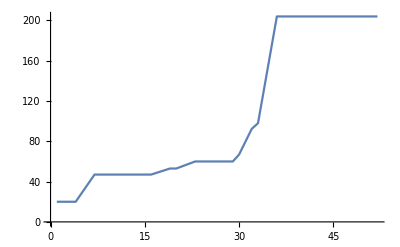

FittedModel[-14.2061+4.34622 x]

```mathematica
topConnectedPersonsVertexOutDegree=gleanWellConnectedPersons[#,"measure"->VertexOutDegree]&/@accumulatingGraphs//Dataset;
vertexOutDegree =tsts =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsVertexOutDegree];
movingAverage=GroupBy[tsts,First->Last,Max]//Values
MovingAverage[%,3]//ListLinePlot
LinearModelFit[movingAverage,{1,x},x]
```

{20,20,20,20,20,20,47,47,47,47,47,47,47,47,47,47,47,47,53,53,53,53,60,60,60,60,60,60,60,60,60,81,98,98,98,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204,204}

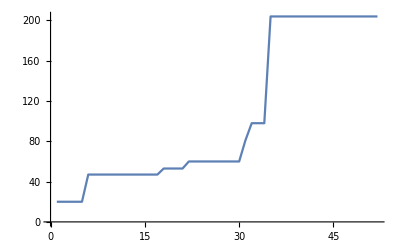

```mathematica
topConnectedPersonsVertexOutDegree=gleanWellConnectedPersons[#,"measure"->VertexOutDegree]&/@accumulatingGraphs//Dataset;
vertexOutDegree =tsts =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsVertexOutDegree];
moveingMedian=GroupBy[tsts,First->Last,Max]//Values
MovingMedian[%,3]//ListLinePlot
```

### VertexInDegree

{1,1,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,2,2,3,3,4,4,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7}

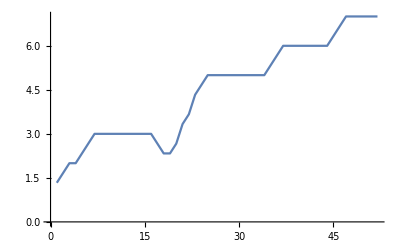

FittedModel[1.44235+0.109167 x]

```mathematica
topConnectedPersonsVertexInDegree=gleanWellConnectedPersons[#,"measure"->VertexInDegree]&/@accumulatingGraphs//Dataset;
vertexInDegree =tsts =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsVertexInDegree];
movingAverage=GroupBy[tsts,First->Last,Max]//Values
MovingAverage[%,3]//ListLinePlot
LinearModelFit[movingAverage,{1,x},x]
```

{1,1,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,2,2,3,3,4,4,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7}

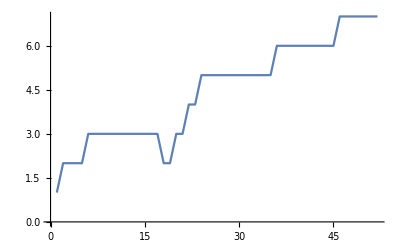

```mathematica
topConnectedPersonsVertexInDegree=gleanWellConnectedPersons[#,"measure"->VertexInDegree]&/@accumulatingGraphs//Dataset;
vertexInDegree =tsts =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsVertexInDegree];
moveingMedian=GroupBy[tsts,First->Last,Max]//Values
MovingMedian[%,3]//ListLinePlot
```

### DegreeCentrality

{20,20,21,21,21,21,47,47,47,47,47,47,47,47,47,47,47,47,53,53,53,53,60,60,60,60,60,60,60,60,60,81,98,98,98,204,204,204,204,204,205,205,205,205,205,205,205,205,205,205,205,205,205,205}

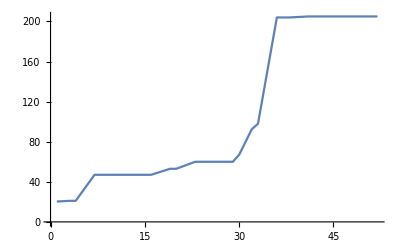

FittedModel[-14.2669+4.36055 x]

```mathematica
topConnectedPersonsDegreeCentrality=gleanWellConnectedPersons[#,"measure"->DegreeCentrality]&/@accumulatingGraphs//Dataset;
vertexDegreeCentrality =tsts =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsDegreeCentrality];
movingAverage=GroupBy[tsts,First->Last,Max]//Values
MovingAverage[%,3]//ListLinePlot
LinearModelFit[movingAverage,{1,x},x]
```

{20,20,21,21,21,21,47,47,47,47,47,47,47,47,47,47,47,47,53,53,53,53,60,60,60,60,60,60,60,60,60,81,98,98,98,204,204,204,204,204,205,205,205,205,205,205,205,205,205,205,205,205,205,205}

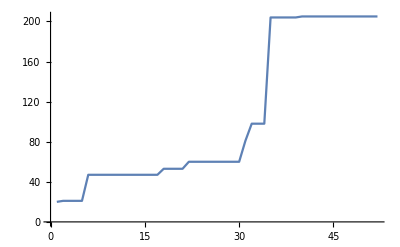

```mathematica
topConnectedPersonsDegreeCentrality=gleanWellConnectedPersons[#,"measure"->DegreeCentrality]&/@accumulatingGraphs//Dataset;
vertexDegreeCentrality =tsts =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsDegreeCentrality];
moveingMedian=GroupBy[tsts,First->Last,Max]//Values
MovingMedian[%,3]//ListLinePlot
```

### BetweennessCentrality

{18.,18.,18.,18.,35.,35.,35.,35.,35.,35.,35.,35.,35.,35.,35.,35.,30.,30.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,215.,215.,215.,215.,215.,214.,214.,214.,214.,370.,512.,511.5,511.5,511.5}

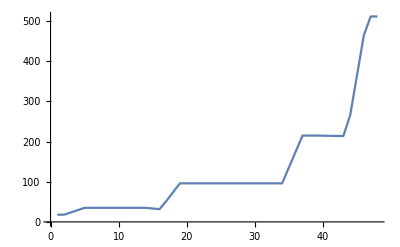

FittedModel[-62.3747+7.64411 x]

```mathematica
topConnectedPersonsBetweennessCentrality=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs//Dataset;
vertexBetweennessCentrality =tsts =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsBetweennessCentrality];
movingAverage=GroupBy[tsts,First->Last,Max]//Values
MovingAverage[%,3]//ListLinePlot
LinearModelFit[movingAverage,{1,x},x]
```

{18.,18.,18.,18.,35.,35.,35.,35.,35.,35.,35.,35.,35.,35.,35.,35.,30.,30.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,96.,215.,215.,215.,215.,215.,214.,214.,214.,214.,370.,512.,511.5,511.5,511.5}

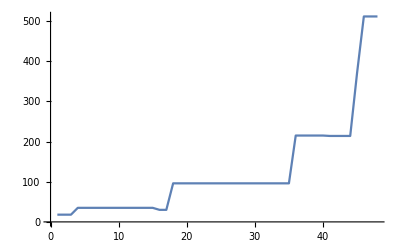

```mathematica
topConnectedPersonsBetweennessCentrality=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs//Dataset;
vertexBetweennessCentrality=tsts =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsBetweennessCentrality];
moveingMedian=GroupBy[tsts,First->Last,Max]//Values
MovingMedian[%,3]//ListLinePlot
```

### MeanNeighborDegree

```mathematica
topConnectedPersonsMeanNeighborDegree=gleanWellConnectedPersons[#,"measure"->MeanNeighborDegree]&/@accumulatingGraphs//Dataset;
vertexMeanNeighborDegree =tsts =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsMeanNeighborDegree];
movingAverage=GroupBy[tsts,First->Last,Max]//Values
MovingAverage[%,3]//ListLinePlot
LinearModelFit[movingAverage,{1,x},x]
```

{20,20,21,21,21,21,47,47,47,47,47,47,47,47,47,47,47,47,53,53,53,53,60,60,60,60,60,60,60,60,60,81,98,98,98,204,204,204,204,204,205,205,205,205,205,205,205,205,205,205,205,205,205,205}

-Graphics-

FittedModel[-14.2669+4.36055 x]

```mathematica
topConnectedPersonsMeanNeighborDegree=gleanWellConnectedPersons[#,"measure"->MeanNeighborDegree]&/@accumulatingGraphs//Dataset;
vertexMeanNeighborDegree=tsts =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsMeanNeighborDegree];
moveingMedian=GroupBy[tsts,First->Last,Max]//Values
MovingMedian[%,3]//ListLinePlot
```

{20,20,21,21,21,21,47,47,47,47,47,47,47,47,47,47,47,47,53,53,53,53,60,60,60,60,60,60,60,60,60,81,98,98,98,204,204,204,204,204,205,205,205,205,205,205,205,205,205,205,205,205,205,205}

-Graphics-

A TimesSeries function for ALL data points for specified SNA metrics, 1964-2017

### VertexOutDegree

```mathematica
topConnectedPersonsVertexOutDegree=gleanWellConnectedPersons[#,"measure"->VertexOutDegree]&/@accumulatingGraphs//Dataset;
vertexOutDegree =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsVertexOutDegree];
allVertexOutDegree=vertexOutDegree[[All,3]];
t=vertexOutDegree[[All,1]];
TimeSeries[allVertexOutDegree,{t}]
```

TimeSeries[…]

### VertextInDegree

```mathematica
topConnectedPersonsVertexInDegree=gleanWellConnectedPersons[#,"measure"->VertexInDegree]&/@accumulatingGraphs//Dataset;
vertexInDegree =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsVertexInDegree];
allVertexInDegree=vertexInDegree[[All,3]];
t=vertexInDegree[[All,1]];
TimeSeries[allVertexInDegree,{t}]
```

TimeSeries[…]

### DegreeCentrality

```mathematica
topConnectedPersonsDegreeCentrality=gleanWellConnectedPersons[#,"measure"->DegreeCentrality]&/@accumulatingGraphs//Dataset;
vertexDegreeCentrality =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsDegreeCentrality];
allDegreeCentrality=vertexDegreeCentrality[[All,3]];
t=vertexDegreeCentrality[[All,1]];
TimeSeries[allDegreeCentrality,{t}]
```

TimeSeries[…]

### BetweennessCentrality

```mathematica
topConnectedPersonsBetweennessCentrality=gleanWellConnectedPersons[#,"measure"->BetweennessCentrality]&/@accumulatingGraphs//Dataset;
vertexBetweennessCentrality =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsDegreeCentrality];
allBetweennessCentrality=vertexBetweennessCentrality[[All,3]];
t=vertexBetweennessCentrality[[All,1]];
TimeSeries[vertexBetweennessCentrality,{t}]
```

TimeSeries[…]

### MeanNeighborhoodDegree

```mathematica
topConnectedPersonsMeanNeighborhoodDegree=gleanWellConnectedPersons[#,"measure"->MeanNeighborhoodDegree]&/@accumulatingGraphs//Dataset;
vertexMeanNeighborhoodDegree =Join@@KeyValueMap[Function[{year,array},Map[Prepend[#,year]&,array]],Normal@topConnectedPersonsMeanNeighborhoodDegree];
allMeanNeighborhoodDegree=vertexMeanNeighborhoodDegree[[All,3]];
t=vertexMeanNeighborhoodDegree[[All,1]];
TimeSeries[allMeanNeighborhoodDegree,{t}]
```

TimeSeries[…]

### Conclusions (needs some more work)

This project revealed that where one received a PhD was more important than where one went to college, with respect to the Mills award. Also, winning the award appears to be related residing at Berkeley, Harvard, Columbia, Princeton, or Chicago (the top five institutions, respectively, won 24 out of 63 winning books). Further, getting a PhD from Harvard, Berkeley, Chicago, and Columbia accounted for 24 out of the 68 winners (respectively, 11, 5, 4, and 4). I did not try more tests, such as TimeSeriesModel or more elaborate tests such as Classify or PredictorFunction. Nor did I have the abilities to explore TimeSeries in more depth. However, this exploratory project does provide some proof of concept. For example, with the LinearModelFit (and TImeSeries) results, these outputs can serve as a heuristic baseline to compare other respective studies (acknowledgements in a select group of prefaces). Unfortunately, testing for nonlinearities and ratios of change were outside of my abilities. I suppose if ratios of change, as a function of time could be mapped, then one may even explore aspects from my original proposal: 1) Dunbar’s 2) Zipf’s, 3) Sarnoff’s, 4) Odlyzko’s, 5) Metcalfe’s, 6) Reed’s, 7) Feigenbaum’s Constant, and any others that measure (rates of) change? And here I really start rambling into Neverland, what about 8) Cellular Automata, 9) Agent Based Modeling, 10) Self-Organized Criticality, 11) Phase Transitions and12) Fractal Geometry? What appropriate Functions [ ] can help elucidate “thank you?” Finally, can key nodes or links be highlighted (visualizations) using a Manipulate Function (for years 1 to n)? If some of these questions can be ascertained from Mills corpus, can these test be replicated with another corpus of “winners”?